```mathematica
encodeID[expr_]:=StringReplace[Developer`EncodeBase64@BinarySerialize@expr,"/"->"~"]
decodeID[expr_]:=BinaryDeserialize@Developer`DecodeBase64ToByteArray@StringReplace[expr,"~"->"/"]
```

```mathematica
ClearAll[getFileNames,fromFileNameGetGeoRange]

getFileNames[folderName_] := 
	FileNames["*.png",FileNameJoin[{NotebookDirectory[],folderName}],Infinity];

fromFileNameGetGeoRange[fileName_] := 
	decodeID[FileBaseName@fileName]["GeoRange"];
```

```mathematica
ClearAll[associateFilesToGeoRange]
associateFilesToGeoRange[fileNames_] := 
	Map[
		File[#] -> fromFileNameGetGeoRange[#] &,
		getFileNames[fileNames]
	]
```

```mathematica
ClearAll[sortPerformance]
sortPerformance[net_,data_] := 
	With[
		{img = Map[Import,data[[All,1]]], correspondingScale = data[[All,2]]},
		SortBy[
			AssociationThread[img,Transpose[{net[img],correspondingScale}]],
			Abs[First[#] - Last[#]]&
		]
	]
```

```mathematica
calculateError[net_,data_] :=(Abs[net[data[[All,1]]]-data[[All,2]]])/data[[All,2]]//Mean
calculateMeanSq[net_,data_] :=(Abs[net[data[[All,1]]]-data[[All,2]]])^2//Mean
```

Length | Training | Validation | Testing
12639 | 2100 | 1050 | 
11854 | 1975 | 990 |

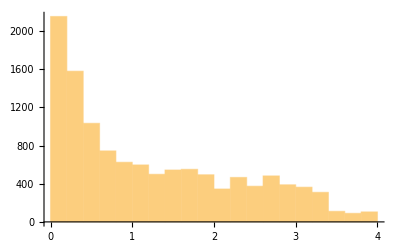
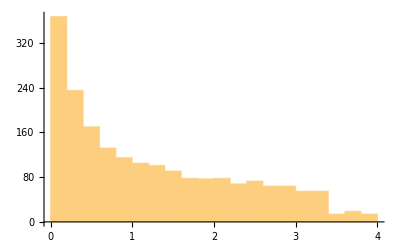
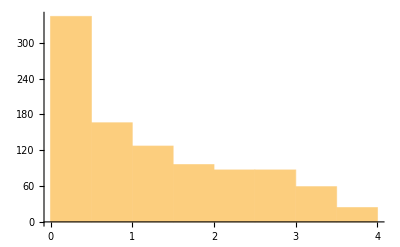
Training Data distribution | Validation Data distribution | Testing Data distribution
-Graphics- | -Graphics- | -Graphics-

```mathematica
ClearAll[training1,validation1,testing1]
ClearAll[trainSmall,validationSmall,testSmall]


training1 = associateFilesToGeoRange["training"];
validation1 = associateFilesToGeoRange["validation"];
testing1 = associateFilesToGeoRange["testing"];

trainSmall = RandomSample@Normal@Select[Association@training1,#<=4&];
validationSmall = RandomSample@Normal@Select[Association@validation1,#<=4&];
testSmall = RandomSample@Normal@Select[Association@testing1,#<=4&];

Grid[
	{{"Length","Training","Validation","Testing"},
	{Length@training1,Length@validation1,Length@testing1},
	{Length@trainSmall,Length@validationSmall,Length@testSmall}}
]



TableForm[
	{{"Training Data distribution","Validation Data distribution","Testing Data distribution"},
	{Histogram[trainSmall[[All,2]]],Histogram[validationSmall[[All,2]]],Histogram[testSmall[[All,2]]]}}
]
```

```mathematica
ClearAll[tnet1]
tnet1 = Import[FileNameJoin[{NotebookDirectory[],"amazonTrainedNet.wlnet"}]]
```

NetChain[<>]

```mathematica
ClearAll[dataset1]
dataset1 = sortPerformance[tnet1,testSmall];
```

```mathematica
dataset1[[1;;4]]  (*Best 3*)
dataset1[[-14;;-11]] (*Worst 3*)
```

<|-Graphics-→{2.7444,2.74455},-Graphics-→{0.468401,0.469929},-Graphics-→{1.07208,1.07445},-Graphics-→{0.414134,0.416545}|>

<|-Graphics-→{1.71616,2.61353},-Graphics-→{3.04402,3.99781},-Graphics-→{2.85387,3.88059},-Graphics-→{0.5854,1.74235}|>

```mathematica
Repeated
```

```mathematica
TableForm[
	{Normal@dataset1[[1;;2]],
	Normal@dataset1[[-12;;-11]]},TableHeadings->{{"Best","Worst"},{"Image        -         Scale  -  Predicted","Image        -         Scale  -  Predicted"}}
]
```

| Image        -         Scale  -  Predicted | Image        -         Scale  -  Predicted
Best | -Graphics-→{2.7444,2.74455} | -Graphics-→{0.468401,0.469929}
Worst | -Graphics-→{2.85387,3.88059} | -Graphics-→{0.5854,1.74235}

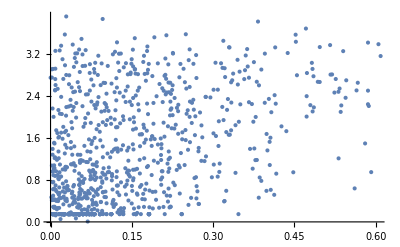

```mathematica
ListPlot[Transpose[{Map[Abs[First[#]-Last[#]]&,Values[dataset1]],Map[First[#]&,Values[dataset1]]}]]
```

```mathematica
calculateError[tnet,testSmall]
```

0.299825